```mathematica
SetDirectory[NotebookDirectory[]];
```

# Floquet analysis for the island-mainland model

## Model

```mathematica
f1[p_,n_]:=p(1-p)(bA(1-n/XA)-ba(1-n/Xa))-p M/n
f2[p_,n_]:=(bA(1-n/XA)p+ba(1-n/Xa)(1-p)-d)n+M
```

## When , solve for

```mathematica
temp=DSolve[{n'[t]==f2[0,n[t]],n[0]==n0},n[t],t][[1]]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{n[t]→1/(2 ba)((ba-d) Xa+√Xa √(4 ba M+(ba-d)^2 Xa) Tanh[(t √(4 ba M+(ba-d)^2 Xa))/(2 √Xa)+ArcTanh[(2 ba n0-ba Xa+d Xa)/(√Xa √(4 ba M+(ba-d)^2 Xa))]])}

```mathematica
TrigToExp[n[t]/.temp]//FullSimplify
```

(ⅇ^((t √(4 ba M+(ba-d)^2 Xa))/(√Xa)) (2 M+(ba-d) n0) Xa+(-2 M+(-ba+d) n0) Xa+n0 √Xa √(4 ba M+(ba-d)^2 Xa)+ⅇ^((t √(4 ba M+(ba-d)^2 Xa))/(√Xa)) n0 √Xa √(4 ba M+(ba-d)^2 Xa))/(d (-1+ⅇ^((t √(4 ba M+(ba-d)^2 Xa))/(√Xa))) Xa-ba (-1+ⅇ^((t √(4 ba M+(ba-d)^2 Xa))/(√Xa))) (-2 n0+Xa)+(1+ⅇ^((t √(4 ba M+(ba-d)^2 Xa))/(√Xa))) √Xa √(4 ba M+(ba-d)^2 Xa))

Rewrite  in a  simplified form:

```mathematica
(*c1=(√(4 ba M+(ba-d)^2 Xa))/(√Xa)*)
(*c2=√Xa √(4 ba M+(ba-d)^2 Xa)*)
```

```mathematica
nhatsimp[t_]:=(ⅇ^(c1 t) (2 M+(ba-d) n0) Xa+(-2 M+(-ba+d) n0) Xa+n0 c2+ⅇ^(c1 t) n0 c2)/(d (-1+ⅇ^(c1 t)) Xa-ba (-1+ⅇ^(c1 t)) (-2 n0+Xa)+(1+ⅇ^(c1 t)) c2)//FullSimplify
```

Find  such that  is periodic:

```mathematica
n0sol=TrigToExp[FullSimplify[Solve[(1-δ)nhatsimp[2π]==nhatsimp[0],n0][[1]]]];
```

```mathematica
nsol[t_]:=(ⅇ^((t √(4 ba M+(ba-d)^2 Xa))/(√Xa)) (2 M+(ba-d) n0) Xa+(-2 M+(-ba+d) n0) Xa+n0 √Xa √(4 ba M+(ba-d)^2 Xa)+ⅇ^((t √(4 ba M+(ba-d)^2 Xa))/(√Xa)) n0 √Xa √(4 ba M+(ba-d)^2 Xa))/(d (-1+ⅇ^((t √(4 ba M+(ba-d)^2 Xa))/(√Xa))) Xa-ba (-1+ⅇ^((t √(4 ba M+(ba-d)^2 Xa))/(√Xa))) (-2 n0+Xa)+(1+ⅇ^((t √(4 ba M+(ba-d)^2 Xa))/(√Xa))) √Xa √(4 ba M+(ba-d)^2 Xa))/.n0sol/.{c1->(√(4 ba M+(ba-d)^2 Xa))/(√Xa),c2->√Xa √(4 ba M+(ba-d)^2 Xa)}
```

## Floquet Multiplier 1

The first Floquet multiplier is given by: .
For this to be less than one, we need only that the exponent be negative, so we look only at the integral:

```mathematica
lam1[pars_]:=NIntegrate[bA(1-nsol[t]/XA)-ba(1-nsol[t]/Xa)-M/nsol[t]/.pars,{t,0,2π}]
```

```mathematica
pars={bA->0.25,ba->0.2,XA->5000,Xa->10000,M->1,δ->0.65,d->0.05};
```

```mathematica
lam1[pars]
```

0.188

### Stability plot

Parameters: , , , ,

```mathematica
BA=0.25;
Ba=0.2;
coords=MeshCoordinates[DiscretizeRegion[ImplicitRegion[0<d<Ba&&0<delt<1-Exp[-2π(BA-d)],{d,delt}],AccuracyGoal->5, MaxCellMeasure->{"Length"->.01}]];
```

```mathematica
Export["coarse_coords.csv",coords,"CSV"];
```

```mathematica
temp={#2,#,lam1[{bA->BA,ba->Ba,XA->5000,Xa->10000,M->1,d->#,δ->#2}]}&@@@coords;
```

```mathematica
Export["stability_lam1_data.csv",temp,"CSV"];
```

## Floquet Multiplier 2

The second Floquet multiplier is given by:

```mathematica
rho2[delt_,pars_]:=(1-delt)Exp[Integrate[ba-d-2 ba/Xa nsol[t]/.{δ->delt}/.pars,{t,0,2π}]]
```

```mathematica
Manipulate[rho2[δ,{ba->0.4,Xa->10000,d->0.2,M->1}],{δ,0,1}]
```

```mathematica
Manipulate[rho2[δ,{ba->0.2,Xa->10000,d->0.05,M->0.5}],{δ,0,1}]
```

```mathematica
temp2={#2,#,rho2[#2,{ba->0.2,Xa->10000,d->#,M->1}]}&@@@coords;
```

```mathematica
Export["stability_rho2_data.csv",temp2,"CSV"];
```

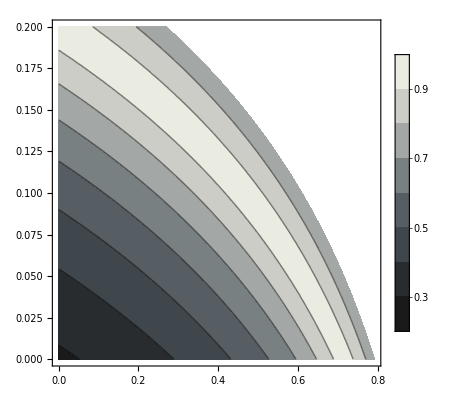

```mathematica
ListContourPlot[temp2,PlotLegends->Automatic,
RegionFunction->Function[{x,y,z},1-Exp[-2π(BA-y)]>x&&z<1],
Frame->{{True,True},{True,True}},
FrameStyle->Directive[Black],
FrameLabel->{Style["",15],Style["",15]},
ColorFunction->ColorData["GrayTones"]]
```

Numerically, we see that .

## Get region of stability

```mathematica
data = Import["stability_lam1_data.csv"];
```

```mathematica
temp=ListContourPlot[data,InterpolationOrder->2,
Contours->{0},
ContourShading->None,
ContourStyle->Directive[Thick,Red],
Frame->{{True,True},{True,True}},
FrameTicks->{{True,False},{True,False}},
FrameLabel->{Style["",15],Style["",15]},
FrameStyle->Directive[Black]];
```

```mathematica
line1=First@Cases[Normal[temp],_Line,Infinity];
line2=Last@Cases[Normal[temp],_Line,Infinity];
```

```mathematica
tval1=ResourceFunction["LeeInterpolatingNodes"][line1[[1]]];
tval2=ResourceFunction["LeeInterpolatingNodes"][line2[[1]]];
```

```mathematica
cc1=Interpolation[Transpose[{tval1,line1[[1]]}],Method->"Spline"];
cc2=Interpolation[Transpose[{tval2,line2[[1]]}],Method->"Spline"];
```

```mathematica
lin1=Table[cc1[s],{s,0,1.03,0.01}];
lin2=Table[cc2[s],{s,0,1.03,0.01}];
```

```mathematica
mr=MeshRegion[DiscretizeRegion[Region[Polygon[Join[lin2,lin1]]]]];
```

# Polymorphism approximation for island-mainland model

## Assume

Solve for

```mathematica
Solve[f1[p,n]==0,p]
```

{{p→0},{p→(bA n^2 Xa-ba n^2 XA+M Xa XA+ba n Xa XA-bA n Xa XA)/(n (bA n Xa-ba n XA+ba Xa XA-bA Xa XA))}}

## Approximate

Plug  into  and solve the resulting differential equation for  to get .

```mathematica
f2[p,n]/.{p->(bA n^2 Xa-ba n^2 XA+M Xa XA+ba n Xa XA-bA n Xa XA)/(n (bA n Xa-ba n XA+ba Xa XA-bA Xa XA))}//Simplify
```

n (bA-d-(bA n)/XA)

```mathematica
DSolve[{n'[t]==n[t] (bA-d-(bA n[t])/XA),n[0]==n0},n[t],t]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n[t]→((bA-d) n0 XA)/(bA n0-ⅇ^((-bA+d) t) (bA (n0-XA)+d XA))}}

Solve for  based on the requirement that

```mathematica
Solve[((1-δ)(bA-d) n0 XA)/(bA n0-ⅇ^((-bA+d) 2π) (bA (n0-XA)+d XA))==n0,n0]//Simplify
```

{{n0→0},{n0→((bA-d) XA (-1+ⅇ^(2 (-bA+d) π)+δ))/(bA (-1+ⅇ^(2 (-bA+d) π)))}}

```mathematica
N0=((bA-d) XA (-1+ⅇ^(2 (-bA+d) π)+δ))/(bA (-1+ⅇ^(2 (-bA+d) π)))//Simplify;
```

```mathematica
Nf=N0/(1-δ)//Simplify;
```

Thus  is given by:

```mathematica
((bA-d) n0 XA)/(bA n0-ⅇ^((-bA+d) t) (bA (n0-XA)+d XA))/.{n0->((bA-d) XA (-1+ⅇ^(2 (-bA+d) π)+δ))/(bA (-1+ⅇ^(2 (-bA+d) π)))}//FullSimplify
```

((bA-d) XA (-1+ⅇ^(2 (-bA+d) π)+δ))/(bA (-1+ⅇ^(2 (-bA+d) π)+δ-ⅇ^((-bA+d) t) δ))

Determine when  is a biologically valid solution, that it, when .

```mathematica
Reduce[{((bA-d) XA (-1+ⅇ^(2 (-bA+d) π)+δ))/(bA (-1+ⅇ^(2 (-bA+d) π)))>0,0<δ<1,XA>0,bA>d>0}]
```

bA>0&&0<d<bA&&XA>0&&0<δ<1-ⅇ^(2 (-bA+d) π)

This is the same as the criteria for a population of exclusively  allele individuals to be viable.

## Approximate

Plug  back into  and solve the resulting differential equation  to get .

takes the form , where  and  are given by:

```mathematica
CoefficientList[f1[p,n]/.{n->((bA-d) XA (-1+ⅇ^(2 (-bA+d) π)+δ))/(bA (-1+ⅇ^(2 (-bA+d) π)+δ-ⅇ^((-bA+d) t) δ))},p]//FullSimplify
```

{0,-ba+bA-(bA M)/(bA XA-d XA)+(bA ⅇ^((-bA+d) t) M δ)/((bA-d) XA (-1+ⅇ^(2 (-bA+d) π)+δ))-((bA-d) (bA Xa-ba XA) (-1+ⅇ^(2 (-bA+d) π)+δ))/(bA Xa (-1+ⅇ^(2 (-bA+d) π)+δ-ⅇ^((-bA+d) t) δ)),ba-bA+((bA-d) (bA Xa-ba XA) (-1+ⅇ^(2 (-bA+d) π)+δ))/(bA Xa (-1+ⅇ^(2 (-bA+d) π)+δ-ⅇ^((-bA+d) t) δ))}

```mathematica
a1[t_]:=-ba+bA-(bA M)/(bA XA-d XA)+(bA ⅇ^((-bA+d) t) M δ)/((bA-d) XA (-1+ⅇ^(2 (-bA+d) π)+δ))-((bA-d) (bA Xa-ba XA) (-1+ⅇ^(2 (-bA+d) π)+δ))/(bA Xa (-1+ⅇ^(2 (-bA+d) π)+δ-ⅇ^((-bA+d) t) δ))
a2[t_]:=ba-bA+((bA-d) (bA Xa-ba XA) (-1+ⅇ^(2 (-bA+d) π)+δ))/(bA Xa (-1+ⅇ^(2 (-bA+d) π)+δ-ⅇ^((-bA+d) t) δ))
```

We know that , where  and

```mathematica
Integrate[a1[t],t]//FullSimplify
```

-ba t+bA (t-(M t)/(bA XA-d XA)-(ⅇ^(2 bA π-bA t+d t) M δ)/((bA-d)^2 XA (ⅇ^(2 d π)+ⅇ^(2 bA π) (-1+δ))))+(-1+(ba XA)/(bA Xa)) Log[ⅇ^((bA-d) t)+ⅇ^((bA-d) (2 π+t)) (-1+δ)-ⅇ^(2 (bA-d) π) δ]

```mathematica
Exp[-ba t+bA (t-(M t)/(bA XA-d XA)-(ⅇ^(2 bA π-bA t+d t) M δ)/((bA-d)^2 XA (ⅇ^(2 d π)+ⅇ^(2 bA π) (-1+δ))))+(-1+(ba XA)/(bA Xa)) Log[ⅇ^((bA-d) t)+ⅇ^((bA-d) (2 π+t)) (-1+δ)-ⅇ^(2 (bA-d) π) δ]]//FullSimplify
```

ⅇ^(-ba t+bA (t-(M t)/(bA XA-d XA)-(ⅇ^(2 bA π-bA t+d t) M δ)/((bA-d)^2 XA (ⅇ^(2 d π)+ⅇ^(2 bA π) (-1+δ))))) (ⅇ^((bA-d) t)+ⅇ^((bA-d) (2 π+t)) (-1+δ)-ⅇ^(2 (bA-d) π) δ)^(-1+(ba XA)/(bA Xa))

```mathematica
b[t_]:=ⅇ^(-ba t+bA (t-(M t)/(bA XA-d XA)-(ⅇ^(2 bA π-bA t+d t) M δ)/((bA-d)^2 XA (ⅇ^(2 d π)+ⅇ^(2 bA π) (-1+δ))))) (ⅇ^((bA-d) t)+ⅇ^((bA-d) (2 π+t)) (-1+δ)-ⅇ^(2 (bA-d) π) δ)^(-1+(ba XA)/(bA Xa))
```

Setting , we solve for :

```mathematica
Solve[(-p0/b0 b2π)/(1+p0/b0 int)==p0,p0]
```

{{p0→0},{p0→(-b0-b2π)/int}}

Hence .

```mathematica
pars={bA->0.25,ba->0.2,XA->500,Xa->1000,M->1,δ->0.65,d->0.05};
```

```mathematica
p0[pars_] := Re[(b[0]-b[2π]/.pars)/NIntegrate[a2[s]b[s]/.pars,{s,0,2π}]]
```

```mathematica
p0[pars]
```

0.451231

### Calculate frequencies

Parameters: , , , ,

```mathematica
BA=0.25;
Ba=0.2;
coords=MeshCoordinates[DiscretizeRegion[ImplicitRegion[0<d<Ba&&0<delt<1-Exp[-2π(BA-d)],{d,delt}],AccuracyGoal->5, MaxCellMeasure->{"Length"->.005}]];
```

```mathematica
Export["fine_coords.csv",coords,"CSV"];
```

```mathematica
temp2={#2,#,If[{#2,#}∈mr,p0[{bA->BA,ba->Ba,XA->5000,Xa->10000,M->1,δ->#2,d->#}],0]}&@@@coords;
```

```mathematica
Export["frequency_data.csv",temp2,"CSV"];
```

# Measuring local adaptation

We define local adaptation generally by:

Which is the difference between the expected fitness of the population of interest in its own habitat and its expected fitness in all possible fitnesses. 
In the case of the island-mainland model, this becomes:

Fitness is given by:
.
Note that since  and  are time dependent, there are different ways to define local adaptation throughout the cycle. We start by considering the local adaptation at the beginning and end of the cycle.

```mathematica
WA[N_,pars_]:=bA-(d+N bA/XA)/.pars
Wa[N_,pars_]:=ba-(d+N ba/Xa)/.pars
```

```mathematica
LF[p_,N_,pars_]:=(p/2)(WA[N,pars]-Wa[N,pars])
```

```mathematica
frequencies=Import["frequency_data.csv"];
```

```mathematica
LFinit={#,#2,If[{#,#2}∈mr,LF[#3,N0/.{bA->BA,ba->Ba,XA->5000,Xa->10000,M->1,δ->#,d->#2},{bA->BA,ba->Ba,XA->5000,Xa->10000,d->#2}],0]}&@@@frequencies;
```

```mathematica
Export["local_adaptation_init.csv",LFinit,"CSV"];
```

```mathematica
LFfinal={#,#2,If[{#,#2}∈mr,LF[#3,Nf/.{bA->BA,ba->Ba,XA->5000,Xa->10000,M->1,δ->#,d->#2},{bA->BA,ba->Ba,XA->5000,Xa->10000,d->#2}],0]}&@@@frequencies;
```

```mathematica
Export["local_adaptation_final.csv",LFfinal,"CSV"];
```

### Stochastic data

Parameters: , , , ,

```mathematica
BA = 0.25;
Ba = 0.2;
xA = 5000;
xa = 10000;
```

```mathematica
temp=Import["stoch_data.csv"];
```

```mathematica
stodata=Drop[temp,1,2];
```

```mathematica
stolf0={#2,#,Chop[LF[Chop[#3],#4,{bA->BA,ba->Ba,XA->xA,Xa->xa,d->#}]]}&@@@stodata;
```

```mathematica
Export["stoch_local_adaptation_init.csv",stolf0,"CSV"];
```

```mathematica
stolff={#2,#,Chop[LF[Chop[#5],#6,{bA->BA,ba->Ba,XA->xA,Xa->xa,d->#}]]}&@@@stodata;
```

```mathematica
Export["stoch_local_adaptation_final.csv",stolff,"CSV"];
```

# Measuring strength of genetic drift

```mathematica
Scoeff[n_,pars_]:=WA[n,pars]-Wa[n,pars]
```

#### When p > 0:

```mathematica
nhat[t_]:=((bA-d) n0 XA)/(bA n0-ⅇ^((-bA+d) t) (bA (n0-XA)+d XA))/.{n0->N0}
```

```mathematica
p1neff[pars_]:=(2π)/NIntegrate[1/(nhat[t]/.pars),{t,0,2π}]
```

#### When p = 0:

```mathematica
p0neff[pars_]:=(2π)/NIntegrate[1/(nsol[t]/.pars),{t,0,2π}]
```

Parameters: , , , ,

```mathematica
BA = 0.25;
Ba = 0.2;
xA = 5000;
xa = 10000;
m = 1;
```

```mathematica
neffdata={#2,#,If[{#2,#}∈mr,p1neff[{bA->BA,ba->Ba,XA->xA,Xa->xa,M->m,δ->#2,d->#}],p0neff[{bA->BA,ba->Ba,XA->xA,Xa->xa,M->m,δ->#2,d->#}]]}&@@@coords;
```

```mathematica
nesdata={#,#2,Abs[Scoeff[#3,{bA->BA,ba->Ba,XA->xA,Xa->xa}]] #3}&@@@neffdata;
```

```mathematica
Export["nes_data.csv",nesdata,"CSV"];
```